```mathematica
TikZInclusion[m_?MatrixQ,x0_,Δx_,Δy_]:=
Module[{rows, columns,matrixEntries,source,target,draw},
rows=Length[m];
columns=Length[m⟦1⟧];
matrixEntries=Flatten[Outer[{#1,#2,m⟦#1,#2⟧}&,Range[rows],Range[columns]],1];
source[r_,c_]:="("<>ToString[N[x0]]<>","<>ToString[N[(c-(columns+1)/2) Δy]]<>")";
target[r_,c_]:="("<>ToString[N[x0+Δx]]<>","<>ToString[N[(r-(rows+1)/2) Δy]]<>")";
draw[{r_,c_,0}]:="";
draw[{r_,c_,1}]:="\draw "<>source[r,c]<>" -- "<>target[r,c]<>";\n";
StringJoin@@(draw/@matrixEntries)<>StringJoin@@("\draw[fill] "<>target[#,1]<>" circle (0.05);\n"&/@Range[rows])
]
```

```mathematica
TikZInclusion[{{1,0},{0,1}},0,1,1]
```

\draw (0.,-0.5) -- (1.,-0.5);
\draw (0.,0.5) -- (1.,0.5);
\draw[fill] (1.,-0.5) circle (0.05);
\draw[fill] (1.,0.5) circle (0.05);

```mathematica
TikZSameDepth[m_?MatrixQ,x0_,Δx_,Δy_]:=
Module[{size,matrixEntries,draw,source,target,control1, control2},
size=Length[m];
matrixEntries=Flatten[Table[{i,j,m⟦i,j⟧},{i,1,size},{j,i,size}],1];
source[r_,c_]:="("<>ToString[N[x0]]<>","<>ToString[N[(c-(size+1)/2) Δy]]<>")";
target[r_,c_]:="("<>ToString[N[x0]]<>","<>ToString[N[(r-(size+1)/2) Δy]]<>")";
control1[r_,c_]:="("<>ToString[N[x0+Δx/2]]<>","<>ToString[N[(-1/2+c-(size+1)/2) Δy]]<>")";
control2[r_,c_]:="("<>ToString[N[x0+Δx/2]]<>","<>ToString[N[(1/2+r-(size+1)/2) Δy]]<>")";
draw[{r_,c_,0}]:="";
draw[{r_,c_,1}]:="\draw "<>source[r,c]<> " .. controls "<>control1[r,c]<>" and "<>control2[r,c]<>" .. "<>target[r,c]<>";\n";
StringJoin@@(draw/@matrixEntries)
]
```

```mathematica
TikZDualData[l_?ListQ,x0_,Δy_]:=Module[{coordinate,draw,total},
total=Length[l];
coordinate[k_]:="("<>ToString[N[x0]]<>","<>ToString[N[(k-(total+1)/2)Δy]]<>")";
draw[k_]:="\draw[red] "<>coordinate[k]<>" to[out=135,in=-135] "<>coordinate[l⟦k⟧]<>";\n";
StringJoin@@(draw/@Cases[Transpose[{l,Range[Length[l]]}],{i_,j_}/;i<j:>i])
]
```

```mathematica
(*TikZDualData[dualPairs_,total_,x0_,Δy_]:=Module[{coordinate,draw},
coordinate[k_]:="("<>ToString[N[x0]]<>","<>ToString[N[(k-(total+1)/2)Δy]]<>")";
draw[k_]:="\draw[red] "<>coordinate[2k-1]<>" to[out=135,in=-135] "<>coordinate[2k]<>";\n";
StringJoin@@(draw/@Range[dualPairs])
]*)
```

```mathematica
tikz="$$\\begin{tikzpicture}\n"<>TikZInclusion[{{1,0},{0,1}},0,1,1]<>TikZSameDepth[{{1,1},{1,1}},1,1,1]<>TikZDualData[1,2,1,1]<>"\\end{tikzpicture}$$"
```

$$\begin{tikzpicture}
\draw (0.,-0.5) -- (1.,-0.5);
\draw (0.,0.5) -- (1.,0.5);
\draw[fill] (1.,-0.5) circle (0.05);
\draw[fill] (1.,0.5) circle (0.05);
\draw (1.,-0.5) .. controls (1.5,-1.) and (1.5,0.) .. (1.,-0.5);
\draw (1.,0.5) .. controls (1.5,0.) and (1.5,0.) .. (1.,-0.5);
\draw (1.,0.5) .. controls (1.5,0.) and (1.5,1.) .. (1.,0.5);
\draw[red] (1.,-0.5) to[out=135,in=-135] (1.,0.5);
\end{tikzpicture}$$

```mathematica
SetDirectory["~/projects/fusionatlas/development/tikz-diagrams"]
```

/Users/scott/projects/fusionatlas/development/tikz-diagrams

```mathematica
DeleteFile["snippet"]
```

```mathematica
WriteString["snippet",tikz]
```

```mathematica
FilePrint["snippet"]
```

$$\begin{tikzpicture}
\draw (0.,-0.5) -- (1.,-0.5);
\draw (0.,0.5) -- (1.,0.5);
\draw[fill] (1.,-0.5) circle (0.05);
\draw[fill] (1.,0.5) circle (0.05);
\draw (1.,-0.5) .. controls (1.5,-1.) and (1.5,0.) .. (1.,-0.5);
\draw (1.,0.5) .. controls (1.5,0.) and (1.5,0.) .. (1.,-0.5);
\draw (1.,0.5) .. controls (1.5,0.) and (1.5,1.) .. (1.,0.5);
\draw[red] (1.,-0.5) to[out=135,in=-135] (1.,0.5);
\end{tikzpicture}$$

```mathematica
Run[
"
cat top-template > document.tex;
cat snippet >> document.tex;
cat bottom-template >> document.tex;
/usr/texbin/pdflatex document.tex;
/usr/texbin/pdfcrop document.pdf --pdftexcmd /usr/texbin/pdftex --verbose --debug > bar 2> foo;
"]
```

0

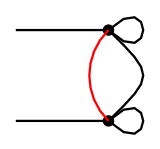

```mathematica
Import["document-crop.pdf"]
```

```mathematica
Run["render"]
```

32512

```mathematica
Run["/bin/bash ls"]
```

32256

```mathematica
Import["!date"]
```

Import::fmtnosup: $Failed is not a supported Import format.

$Failed

```mathematica
pdf
```